Get the photon flux of generic spectrum. PPPC uses GeV. Output should be MeV to match the Fermi analysis.

```mathematica
Get["/Users/austingottfredson/Indirect-Dark-Matter-Detection/dlNdlxEW.m"];
```

```mathematica
primary="b";
j0=10^18;
sigmav0=10^-25;
```

```mathematica
dndlx[mdm_,x_,primary_]:=10^(dlNdlxIEW[primary->"γ"][mdm,Log[10,x]]);
```

```mathematica
ebin=With[{i:=10^xp},Table[i,{xp,1,5,0.1}]]; (* Energy in GeV *)
```

```mathematica
(* Integration limits should be in GeV for PPPC documentation *)n[mdm_,bin_,primary_]:=NIntegrate[dndlx[mdm,energy/mdm,primary]/(Log[10] energy),{energy,ebin[[bin]],ebin[[bin + 1]]}]; (* Result should be the number of photons for a slice of energy *)
```

```mathematica
photonflux[mdm_,primary_]:=Table[{(ebin[[bin]]+ebin[[bin+1]])/2,1/(4 Pi)sigmav0/(2 mdm^2) n[mdm,bin,primary] j0},{bin,1,Length[ebin]-1}]
```

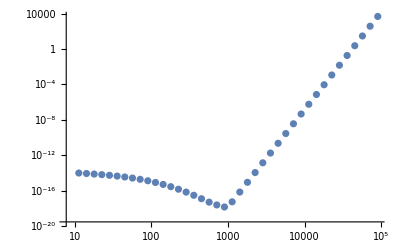

```mathematica
ListLogLogPlot[photonflux[1000,primary]]
```

```mathematica
dndlx[1000,.5,primary]
```

```mathematica
photonflux[1000,primary]
```

{{11.2946,9.64498×10^-15},{14.2191,8.52332×10^-15},{17.9008,7.4243×10^-15},{22.5357,6.38606×10^-15},{28.3708,5.3643×10^-15},{35.7167,4.37363×10^-15},{44.9647,3.44618×10^-15},{56.6072,2.61272×10^-15},{71.2643,1.88976×10^-15},{89.7164,1.29211×10^-15},{112.946,8.30237×10^-16},{142.191,4.9768×10^-16},{179.008,2.77015×10^-16},{225.357,1.42729×10^-16},{283.708,6.76692×10^-17},{357.167,2.95079×10^-17},{449.647,1.21153×10^-17},{566.072,4.94598×10^-18},{712.643,2.38739×10^-18},{897.164,1.40235×10^-18},{1129.46,5.38003×10^-18},{1421.91,6.82074×10^-17},{1790.08,8.64726×10^-16},{2253.57,1.09629×10^-14},{2837.08,1.38986×10^-13},{3571.67,1.76205×10^-12},{4496.47,2.2339×10^-11},{5660.72,2.83212×10^-10},{7126.43,3.59052×10^-9},{8971.64,4.55202×10^-8},{11294.6,5.771×10^-7},{14219.1,7.3164×10^-6},{17900.8,0.0000927565},{22535.7,0.00117596},{28370.8,0.0149086},{35716.7,0.18901},{44964.7,2.39624},{56607.2,30.3793},{71264.3,385.145},{89716.4,4882.82}}